# Fitting the binding curve

## Reading the data

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
x=BinaryReadList["x2.dat","Real32"];
y=BinaryReadList["y2.dat","Real32"];
```

```mathematica
x=BinaryReadList["x3.dat","Real32"];
y=BinaryReadList["y3.dat","Real32"];
```

```mathematica
x=BinaryReadList["x4.dat","Real32"];
y=BinaryReadList["y4.dat","Real32"];
```

```mathematica
scatter=Table[{x[[i]],y[[i]]},{i,1,Length[x]}];
```

## Lennard-Jonnes (doesn’t work so well)

```mathematica
Clear[ϵ,σ]
nlm=Normal[NonlinearModelFit[scatter,4ϵ((σ/r)^12-(σ/r)^6),{ϵ,σ},r]]
```

0.398034 (0.0000290955/r^12-0.00539402/r^6)

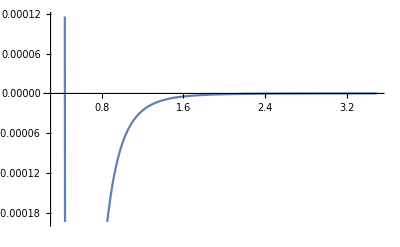

```mathematica
Clear[f]
f[r_]:=0.010619523843508963 (0.000053110959268918895/r^12-0.007287726618700713/r^6)
Show[Plot[f[r],{r,0.3,3.5}],ListPlot[scatter]]
```

## Morse: model 30

```mathematica
nlm=Normal[NonlinearModelFit[scatter,De(Exp[-2a(r-re)]-2Exp[-a(r-re)]),{De,a,re},r]]
```

0.109796 (ⅇ^(-5.64731 (-0.70696+r))-2 ⅇ^(-2.82366 (-0.70696+r)))

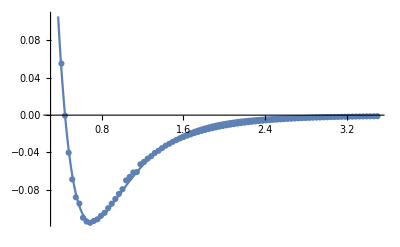

```mathematica
Clear[f]
f[r_]:=0.11431618298122725 (ⅇ^(-5.246522905831081 (-0.706041902090514+r))-2 ⅇ^(-2.6232614529155405 (-0.706041902090514+r)))
Show[Plot[f[x],{x,0.3,3.5}],ListPlot[scatter]]
```

## Morse: model 34

```mathematica
nlm=Normal[NonlinearModelFit[scatter,De(Exp[-2a(r-re)]-2Exp[-a(r-re)]),{De,a,re},r]]
```

1.16489 (ⅇ^(-5.06289 (-0.473807+r))-2 ⅇ^(-2.53145 (-0.473807+r)))

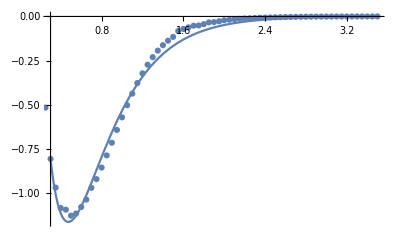

```mathematica
Clear[f]
f[r_]:=1.1648862789641146 (ⅇ^(-5.062890344916867 (-0.4738073301632655+r))-2 ⅇ^(-2.5314451724584335 (-0.4738073301632655+r)))
Show[Plot[f[x],{x,0.3,3.5}],ListPlot[scatter]]
```